```mathematica
Residue[ ( -Zeta'[s]/Zeta[s]) x^s s^(-1),{s,1}]
```

x

```mathematica
Residue[ ( (-Zeta'[s])/Zeta[s]) x^s s^(-1),{s,1}]
```

x

```mathematica
Residue[ (Zeta[s]^3) x^s s^(-1),{s,1}]
```

1/2 (2 x-6 EulerGamma x+6 EulerGamma^2 x-2 x Log[x]+6 EulerGamma x Log[x]+x Log[x]^2-6 x StieltjesGamma[1])

```mathematica
Residue[ ( (-Zeta'[s])^2/Zeta[s]) x^s s^(-1),{s,1}]
```

1/2 (2 x+2 EulerGamma x+2 EulerGamma^2 x-2 x Log[x]-2 EulerGamma x Log[x]+x Log[x]^2+6 x StieltjesGamma[1])

```mathematica
Residue[ ( (Zeta''[s])/Zeta[s]) x^s s^(-1),{s,1}]
```

-2 (x+EulerGamma x-x Log[x])

```mathematica
Residue[ ( (Zeta'''[s])/Zeta[s]) x^s s^(-1),{s,1}]
```

-3 (2 x+2 EulerGamma x+2 EulerGamma^2 x-2 x Log[x]-2 EulerGamma x Log[x]+x Log[x]^2+2 x StieltjesGamma[1])

```mathematica
Residue[ (( 1/Zeta[s] - 1)^2) x^s s^(-1),{s,1}]
```

0

```mathematica
Residue[ (( Zeta[s] - 1)^2) x^s s^(-1),{s,1}]
```

-3 x+2 EulerGamma x+x Log[x]

```mathematica
Residue[ (( Zeta[s] )^2) x^s s^(-1),{s,1}]
```

-x+2 EulerGamma x+x Log[x]

```mathematica
Residue[ (( Zeta[s] - 1)^3) x^s s^(-1),{s,1}]
```

1/2 (14 x-18 EulerGamma x+6 EulerGamma^2 x-8 x Log[x]+6 EulerGamma x Log[x]+x Log[x]^2-6 x StieltjesGamma[1])

```mathematica
Residue[ (( Zeta[s] )^3) x^s s^(-1),{s,1}]
```

1/2 (2 x-6 EulerGamma x+6 EulerGamma^2 x-2 x Log[x]+6 EulerGamma x Log[x]+x Log[x]^2-6 x StieltjesGamma[1])

```mathematica
Residue[ (( Zeta[s])^(1/2)) x^s s^(-1),{s,1}]
```

Residue[(x^s √Zeta[s])/s,{s,1}]

```mathematica
CoefficientList[Series[(x+1)^(1/2),{x,0,20}],x]
```

```mathematica
sq:= sq={1,1/2,-1/8,1/16,-5/128,7/256,-21/1024,33/2048,-429/32768,715/65536,-2431/262144,4199/524288,-29393/4194304,52003/8388608,-185725/33554432,334305/67108864,-9694845/2147483648,17678835/4294967296,-64822395/17179869184,119409675/34359738368,-883631595/274877906944}
```

```mathematica
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}];D2[n_,0]:=D2[n,0]=1
DD[n_,k_]:=DD[n,k] = Sum[DD[Floor[n/j],k-1],{j,1,n}];DD[n_,0]:=DD[n,0] =1
d[n_,z_]:=Product[Pochhammer[z,a=p[[2]]]/a!,{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
Da[n_,z_]:=Sum[ d[j,z],{j,1,n}]
T1:= T1=Table[ Residue[ ( Zeta[s])^k x^s s^(-1),{s,1}],{k,1,15}]
T2:= T2=Table[ Residue[ ( Zeta[s]-1)^k x^s s^(-1),{s,1}],{k,1,15}]
T2cal:= T2cal=Table[T2[[k]]/. x->1,{k,1,15}]
Ap[n_,k_] := (-1)^(k)(1-Gamma[k,-Log[n]]/Gamma[k])
```

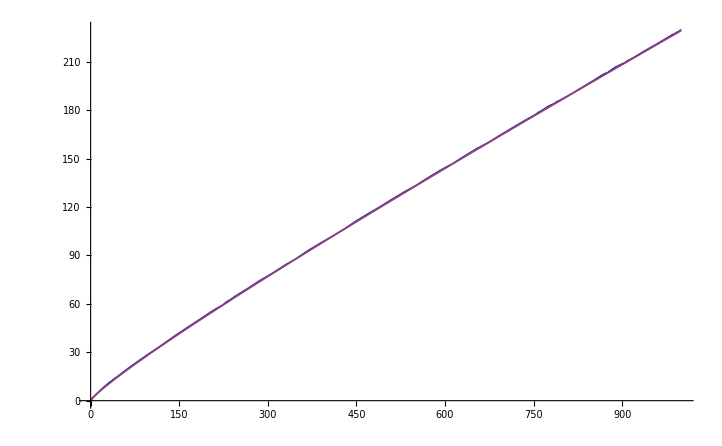

```mathematica
Plot[ {Da[n,.5], TT[n]},{n,1,1000}]
```

```mathematica
D2e[n_, k_] :=D2e[n,k]=(T2[[k]]/. x->n)-T2cal[[k]]
```

```mathematica
N[D2e[100,15]]
```

0.174724

```mathematica
sq[[21]]
```

-883631595/274877906944

```mathematica
Series[(x+1)^(1/2),{x,0,20}]
```

1+x/2-x^2/8+x^3/16-(5 x^4)/128+(7 x^5)/256-(21 x^6)/1024+(33 x^7)/2048-(429 x^8)/32768+(715 x^9)/65536-(2431 x^10)/262144+(4199 x^11)/524288-(29393 x^12)/4194304+(52003 x^13)/8388608-(185725 x^14)/33554432+(334305 x^15)/67108864-(9694845 x^16)/2147483648+(17678835 x^17)/4294967296-(64822395 x^18)/17179869184+(119409675 x^19)/34359738368-(883631595 x^20)/274877906944+O[x]^21

```mathematica
TT[n_] := Sum[ D2e[n,k] sq[[k+1]],{k,1,15}]
```

```mathematica
N[TT[100]]
```

28.9118

```mathematica
Da[100,.5]
```

29.4385

```mathematica
CoefficientList[Series[(x+1)^(-1/2),{x,0,20}],x]
```

```mathematica
sq2:=sq2={1,-1/2,3/8,-5/16,35/128,-63/256,231/1024,-429/2048,6435/32768,-12155/65536,46189/262144,-88179/524288,676039/4194304,-1300075/8388608,5014575/33554432,-9694845/67108864,300540195/2147483648,-583401555/4294967296,2268783825/17179869184,-4418157975/34359738368,34461632205/274877906944}
```

```mathematica
TT2[n_] := Sum[ D2e[n,k] sq2[[k+1]],{k,1,15}]
```

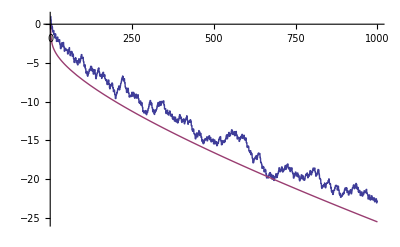

```mathematica
Plot[ {Da[n,-.5], TT2[n]},{n,1,1000}]
```

```mathematica
CoefficientList[Series[(x+1)^(11/3),{x,0,20}],x]
```

```mathematica
sq4:=sq4={1,11/3,44/9,220/81,110/243,-22/729,44/6561,-44/19683,55/59049,-715/1594323,1144/4782969,-1976/14348907,10868/129140163,-20900/387420489,41800/1162261467,-259160/10460353203,550715/31381059609,-1198615/94143178827,23972300/2541865828329,-54253100/7625597484987,124782130/22876792454961}
```

```mathematica
TT3[n_] := Sum[ D2e[n,k] sq4[[k+1]],{k,1,15}]
```

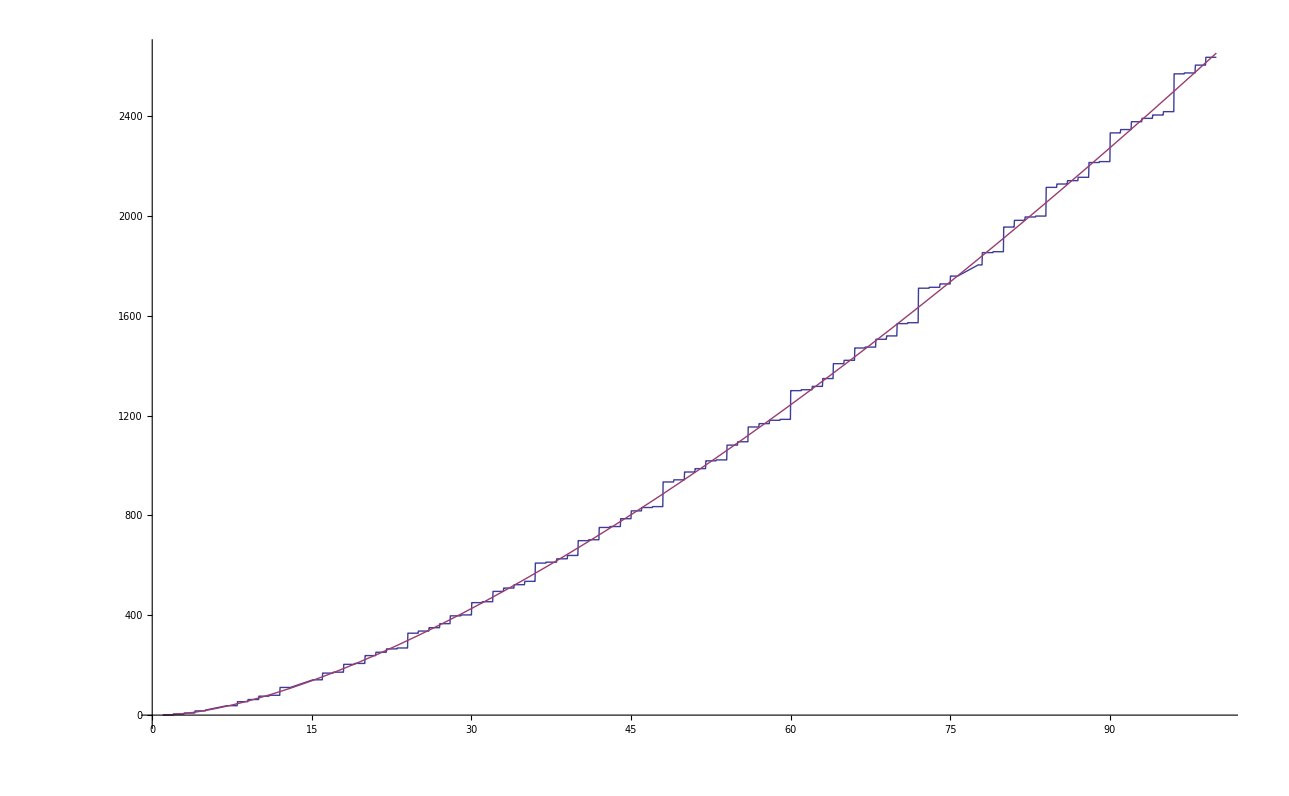

```mathematica
Plot[ {Da[n,11/3], TT3[n]},{n,1,100}]
```

```mathematica
FullSimplify[TT3[100]]
```

$Aborted

```mathematica
Residue[ (( 1/Zeta[s]-1)^3) x^s s^(-1),{s,ZetaZero[1]}]
```

1/(2 ZetaZero[1]^3 Zeta'[ZetaZero[1]]^5)x^ZetaZero[1] (2 Zeta'[ZetaZero[1]]^2-2 Log[x] ZetaZero[1] Zeta'[ZetaZero[1]]^2+Log[x]^2 ZetaZero[1]^2 Zeta'[ZetaZero[1]]^2+6 ZetaZero[1] Zeta'[ZetaZero[1]]^3-6 Log[x] ZetaZero[1]^2 Zeta'[ZetaZero[1]]^3+6 ZetaZero[1]^2 Zeta'[ZetaZero[1]]^4+3 ZetaZero[1] Zeta'[ZetaZero[1]] Zeta''[ZetaZero[1]]-3 Log[x] ZetaZero[1]^2 Zeta'[ZetaZero[1]] Zeta''[ZetaZero[1]]+6 ZetaZero[1]^2 Zeta'[ZetaZero[1]]^2 Zeta''[ZetaZero[1]]+3 ZetaZero[1]^2 Zeta''[ZetaZero[1]]^2-ZetaZero[1]^2 Zeta'[ZetaZero[1]] Zeta^(3)[ZetaZero[1]])

```mathematica
Expand[N[Residue[ (1/Zeta[s]-1)^5 x^s s^(-1),{s,-}]]]
```

```mathematica
-(1.4336164867684953*^6)/x^12-(1.000945863241807*^6 Log[x])/x^12-(296294.1074337942 Log[x]^2)/x^12-(43931.56901950145 Log[x]^3)/x^12-(3424.5090584396494 Log[x]^4)/x^12/. x->30
```

-1.9668×10^-11

```mathematica
-(2.6293790206287857*^10)/x^4+(2.3362281125511642*^10 Log[x])/x^4-(1.0492298802763643*^10 Log[x]^2)/x^4+(2.0378708460337496*^9 Log[x]^3)/x^4-(3.2112743289672685*^8 Log[x]^4)/x^4/. x->30
```

-38275.6

```mathematica
(6.323835876938515*^8)/x^2-(4.285452073963622*^8 Log[x])/x^2+(1.1648048622212459*^8 Log[x]^2)/x^2-(1.5116183750507852*^7 Log[x]^3)/x^2+(796035.2726571471 Log[x]^4)/x^2/. x->30
```

37835.9

```mathematica
-(1.3411724350748308*^10)/x^8-(1.1006033172471167*^10 Log[x])/x^8-(4.783694263329197*^9 Log[x]^2)/x^8-(8.32892837809015*^8 Log[x]^3)/x^8-(1.3094353790709832*^8 Log[x]^4)/x^8/. x->30
```

-0.238497

```mathematica
(5.3471497797748664*^13 (-0.00025082006121236776-0.00020582990239212187 Log[x]-0.00008946250732349238 Log[x]^2-0.000015576388769945447 Log[x]^3-2.4488473916025503*^-6 Log[x]^4))/x^8/. x->30
```

-0.238497

```mathematica
(2.958409010521708*^10 (-0.001956045140633667-0.0020025789009419587 Log[x]-0.0005729504086642285 Log[x]^2-0.0001472342287128506 Log[x]^3))/x^8/. x->30
```

-0.000955393

```mathematica
N[Series[ (1/(x+1))^(3/2),{x,0,20}]]
```

1.-1.5 (x+0.)+1.875 (x+0.)^2-2.1875 (x+0.)^3+2.46094 (x+0.)^4-2.70703 (x+0.)^5+2.93262 (x+0.)^6-3.14209 (x+0.)^7+3.33847 (x+0.)^8-3.52394 (x+0.)^9+3.70014 (x+0.)^10-3.86833 (x+0.)^11+4.02951 (x+0.)^12-4.18449 (x+0.)^13+4.33393 (x+0.)^14-4.4784 (x+0.)^15+4.61835 (x+0.)^16-4.75418 (x+0.)^17+4.88624 (x+0.)^18-5.01483 (x+0.)^19+5.1402 (x+0.)^20+O[x+0.]^21

```mathematica
Sum[ (-1)^k (1/Zeta[s]-1)^k,{k,0,Infinity}]
```

Zeta[s]

```mathematica
Eta[s_] := (1-2^(1-s))Zeta[s]
```

```mathematica
N[Eta[ZetaZero[3]+1]]
```

0.810643-0.359653 ⅈ

```mathematica
pr[x_, t_] :=Sum[N[Residue[ (1/Zeta[s]-1)^k x^s s^(-1),{s,-2t}]],{k,1,16}]
```

```mathematica
pr[30,1]
```

Sum::itraw: Raw object 1 cannot be used as an iterator.

NSum::itraw: Raw object 1 cannot be used as an iterator.

NSum[Residue[((1/Zeta[s]-1)^1 30^s)/s,{s,-2 1}],{1,1,16}]